# 1-D universal estimator using DNN

## Generating data (without duplicating θ and logging the histogram)

Generates synthetic data for DNN :

Arguments:
	n: number of samples drawn for a given θ 
	M: number of different θ generated in the range [min_θ, max_θ]
	f: the distribution function for generating samples. f(θ, N) returns N observations using parameter θ
	range: range of the dist parameter θ
	bins: number of bins in the histograms generated from samples: 
Return:
	a table of associations(one row per sample): histogram->θ

```mathematica
GenerateData[M_, n_, f_, range_, bins_:-1]:=
	Module[{params, samples, nbins, MAXBINS},
		params=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
		(*generate M different random initparameters in the range [min_θ,max_θ]*) 
		samples=Table[f[params[[i]],n],{i,1,M}];
		(*generate M distributions, each distribution has n number/data*, now we have M*n data*)
		MAXBINS=5000;
		nbins=If[bins>0,bins,Min[MAXBINS, Ceiling[Max[samples]]+1](*Ceiling[Max[samples]]+2] if using zero padding*)];
		h[x_]:=HistogramList[x,{0,nbins,1}][[2]]; (*without using log10(x+1)*)
		Table[h@samples[[i]]->params[[i]], {i,1,M}]  
	
	]
```

## Example of generated data

```mathematica
(*f[å_,N_]:=RandomVariate[WaringYuleDistribution[å],N];
Print[GenerateData[5,10,f,{2,3}]//TableForm];*)
```

{6,3,0,1}→2.67938
{6,0,4,0}→2.21798
{7,1,1,1}→2.25193
{7,2,1,0}→2.76568
{6,1,1,2}→2.16986

## DNN

Generate a DNN for predicting the parameter θ from the distribution histogram
The input size is the number of bins in the input histogram, the output is a scalar predicting the parameter used to generate the input sample.

```mathematica
CreateNet[bins_]:=( 
NetChain[{
LinearLayer[bins],  
BatchNormalizationLayer[],  (*batch normaliztiozion*)
ElementwiseLayer[Ramp], (*Ramp is the relu*)

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 

LinearLayer[1]
},
"Input"->bins, 
"Output" -> "Scalar"]
)
```

## 1-D universal estimator using DNN

Given a distribution  dist(x|θ) and the range for the parameter θ,  
UniversalEstimator returns an Estimator function for predicting the parameter θ given an input sample S.

```mathematica
UniversalEstimator[dist_, range_]:=Module[{g, M, n, trainSet, bins, valSet ,net, trained, model, h},
(*define a sample generator*)
g[θ_,n_] := RandomVariate[dist[θ],n];

(*train a NN for predicting the parameter θ *)
(*generate learning samples in the the given parameter range*)
M = 10000; 
n = 2048;   (*number of observations in each sample*)
trainSet=GenerateData[M,n, g, range];
bins = Length@trainSet[[1]][[1]]; (*use the same number of bins for the validation set*)
valSet=GenerateData[M/2,n, g, range, bins];

(*Create and train the NN*)
net = NetInitialize@CreateNet[bins];

trained=NetTrain[
net,
trainSet,
All,
ValidationSet->valSet, 
TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->500|>, (*using loss criterion to prevent overfitting*)
Method->"ADAM" ,
BatchSize->1024
];

Print[trained];  (*print the training result*)

model = trained["TrainedNet"];

(*define a function for generating a histogram with nbins from an input sample )*)
h[x_]:=HistogramList[x,{0,bins,1}][[2]];

(*return an Estimator which is a fucntion map sample to a parameter*)
Function[{sample}, (
(*return a prediction of the parameter θ*)
model[h@sample]
)]
]
```

## Experiment of universal estimator with DNN

n : number of samples drawn for a given θ 
M : number of different θ generated in the range [min_θ, max_θ]
S : number of samples per θ

```mathematica
RunExperiment[dist_, range_]:= Module[{estimator, g, adjuster, params, n, samples, Θ, Θhat, e, TestSet, M, initΘ, expansion,S},
(*generate an Estimator for dist*)
estimator = UniversalEstimator[dist, range];
(*define the size of the test set*)
M = 20;
S = 10；
n = 2048;

initΘ=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
(*generate M different random initΘ in the range [min_θ,max_θ]*)
expansion[j_]:=Table[initΘ[[j]],S]; 
(*define an expansion function for duplicating the initΘ*)
Θ=Flatten[Table[expansion[w],{w,1,M}]];
(*increase the number of each different parameters to S, now we have M*S Θ *)		
g[θ_,a_] := RandomVariate[dist[θ],a];
(*create M*S test samples*)
samples = Table[g[Θ[[i]], n], {i,1,M*S,1 }];

(*predict the parameter for each sample*)
Θhat = Table[estimator[samples[[i]]], {i,1,M*S,1 }];

(*evaluate prediction errors*)

e = Table[Abs[Θ[[i]] - Θhat[[i]]], {i,1,M*S,1 }];

Print["θ: ",Θ];
Print["θ̂: ",Θhat];
Print["abs(θ-θ̂): ",e];
Print["RMSE:",RootMeanSquare[e]];

(*return true parameters and predicted errors*)
{Θ, e}
]
```

## Run the experiment for different distributions

### Yule-Simon Distribution

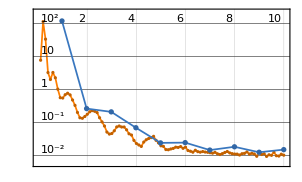
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:100  rounds:10  time:2.2min  examples/s:789
data | ,,  training examples:10000  validation examples:5000  processed examples:102400  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:1.05×10^-2
validation | ,,  loss:1.5×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {2.27331,2.27331,2.27331,2.27331,2.27331,2.27331,2.27331,2.27331,2.27331,2.27331,2.18472,2.18472,2.18472,2.18472,2.18472,2.18472,2.18472,2.18472,2.18472,2.18472,2.62651,2.62651,2.62651,2.62651,2.62651,2.62651,2.62651,2.62651,2.62651,2.62651,2.02589,2.02589,2.02589,2.02589,2.02589,2.02589,2.02589,2.02589,2.02589,2.02589,2.86767,2.86767,2.86767,2.86767,2.86767,2.86767,2.86767,2.86767,2.86767,2.86767,2.13192,2.13192,2.13192,2.13192,2.13192,2.13192,2.13192,2.13192,2.13192,2.13192,2.23526,2.23526,2.23526,2.23526,2.23526,2.23526,2.23526,2.23526,2.23526,2.23526,2.71203,2.71203,2.71203,2.71203,2.71203,2.71203,2.71203,2.71203,2.71203,2.71203,2.1948,2.1948,2.1948,2.1948,2.1948,2.1948,2.1948,2.1948,2.1948,2.1948,2.33956,2.33956,2.33956,2.33956,2.33956,2.33956,2.33956,2.33956,2.33956,2.33956,2.71819,2.71819,2.71819,2.71819,2.71819,2.71819,2.71819,2.71819,2.71819,2.71819,2.17454,2.17454,2.17454,2.17454,2.17454,2.17454,2.17454,2.17454,2.17454,2.17454,2.18742,2.18742,2.18742,2.18742,2.18742,2.18742,2.18742,2.18742,2.18742,2.18742,2.37625,2.37625,2.37625,2.37625,2.37625,2.37625,2.37625,2.37625,2.37625,2.37625,2.41397,2.41397,2.41397,2.41397,2.41397,2.41397,2.41397,2.41397,2.41397,2.41397,2.20467,2.20467,2.20467,2.20467,2.20467,2.20467,2.20467,2.20467,2.20467,2.20467,2.03205,2.03205,2.03205,2.03205,2.03205,2.03205,2.03205,2.03205,2.03205,2.03205,2.04978,2.04978,2.04978,2.04978,2.04978,2.04978,2.04978,2.04978,2.04978,2.04978,2.64877,2.64877,2.64877,2.64877,2.64877,2.64877,2.64877,2.64877,2.64877,2.64877,2.08128,2.08128,2.08128,2.08128,2.08128,2.08128,2.08128,2.08128,2.08128,2.08128}

θ̂: {2.29387,2.31252,2.3218,2.1892,2.47137,2.41427,2.25633,2.54951,2.22354,2.45058,2.15874,2.31789,2.1845,2.23256,2.26212,2.15276,2.29783,2.28019,2.19021,2.07136,2.74495,2.66946,2.56107,2.53429,2.74667,2.75622,2.65081,2.81919,2.77996,2.76994,2.19155,2.10259,2.17932,2.17747,2.07319,2.13647,2.20609,2.09567,2.11806,2.14384,2.91127,2.8733,2.92631,2.84549,2.87241,2.7175,2.84566,2.87484,2.90268,2.84613,2.22961,2.17087,2.2197,2.19146,2.17322,2.07086,2.23591,2.19594,2.2711,2.21011,2.29439,2.48289,2.31174,2.55657,2.21973,2.13283,2.2173,2.2621,2.27741,2.38082,2.76135,2.72649,2.80591,2.67269,2.84283,2.71627,2.76111,2.62922,2.79102,2.78501,2.27818,2.30194,2.16238,2.26533,2.16991,2.09503,2.30373,2.24964,2.29399,2.37784,2.40393,2.46674,2.42265,2.3927,2.50961,2.37654,2.66128,2.36944,2.58262,2.42176,2.62199,2.8309,2.80557,2.6192,2.76183,2.85054,2.74478,2.80732,2.77017,2.75631,2.15277,2.2728,2.17552,2.13036,2.31966,2.23531,2.23549,2.2786,2.30388,2.17115,2.17963,2.16732,2.14865,2.16616,2.18765,2.3116,2.19295,2.23701,2.1723,2.26079,2.26106,2.54368,2.45009,2.42154,2.25105,2.58529,2.49908,2.59675,2.39763,2.4785,2.48452,2.41549,2.46358,2.49931,2.58749,2.66431,2.37299,2.38986,2.66449,2.4344,2.30291,2.26628,2.11935,2.22421,2.27435,2.20579,2.22201,2.22771,2.21689,2.21935,2.13308,2.28319,2.09559,2.20282,2.20232,2.1197,2.06707,2.1352,2.14117,2.12484,2.22565,2.1438,2.14873,2.14465,2.13365,2.13511,2.19436,2.19187,2.12482,2.17568,2.79498,2.75925,2.72789,2.76762,2.76227,2.78745,2.74372,2.75383,2.77042,2.72965,2.18971,2.20422,2.22306,2.1154,2.32142,2.23918,2.15254,2.25133,2.11691,2.18297}

abs(θ-θ̂): {0.0205593,0.0392136,0.0484881,0.0841053,0.198064,0.140965,0.0169757,0.276199,0.0497708,0.177271,0.025975,0.133171,0.000220535,0.0478389,0.0774081,0.0319519,0.113111,0.0954695,0.00549174,0.113357,0.118444,0.0429534,0.0654345,0.0922127,0.120168,0.12971,0.0243041,0.192682,0.153459,0.143439,0.165663,0.0767041,0.153437,0.151585,0.0473068,0.110588,0.180208,0.0697826,0.0921729,0.11795,0.0436072,0.00563543,0.0586387,0.0221785,0.00474684,0.150167,0.0220109,0.00717561,0.0350119,0.0215414,0.0976858,0.0389514,0.0877759,0.0595343,0.0412965,0.0610607,0.10399,0.0640218,0.139181,0.0781917,0.0591295,0.247627,0.0764756,0.321309,0.0155327,0.102437,0.0179648,0.0268366,0.0421505,0.145554,0.0493161,0.0144521,0.0938775,0.0393425,0.130799,0.00423686,0.0490729,0.0828188,0.0789875,0.0729741,0.0833775,0.10714,0.0324284,0.070522,0.0248934,0.0997785,0.108923,0.0548397,0.0991825,0.183036,0.0643695,0.127177,0.083088,0.0531352,0.170051,0.0369747,0.32172,0.0298772,0.24306,0.0821975,0.0962025,0.112704,0.0873767,0.0989899,0.0436393,0.132353,0.0265842,0.0891262,0.0519777,0.0381156,0.0217708,0.0982608,0.000981004,0.0441833,0.145112,0.0607695,0.0609464,0.104054,0.12934,0.00339612,0.00779202,0.0201011,0.0387771,0.0212596,0.000230289,0.124171,0.0055301,0.0495832,0.0151215,0.073363,0.11519,0.167437,0.0738416,0.0452938,0.125195,0.20904,0.122834,0.220503,0.0213883,0.102254,0.0705478,0.00151464,0.0496032,0.0853383,0.17352,0.250335,0.0409885,0.0241103,0.250514,0.0204289,0.0982383,0.0616153,0.0853144,0.0195421,0.0696856,0.00112591,0.0173415,0.0230428,0.0122229,0.0146857,0.101031,0.251143,0.06354,0.170773,0.170275,0.0876563,0.0350232,0.103155,0.109129,0.092794,0.175874,0.0940198,0.098946,0.0948669,0.0838732,0.0853275,0.144577,0.142085,0.0750362,0.1259,0.146215,0.110482,0.079121,0.118847,0.113502,0.138681,0.0949484,0.105065,0.121649,0.0808786,0.108429,0.122943,0.141783,0.0341181,0.240136,0.157894,0.0712611,0.170051,0.0356297,0.101693}

RMSE:0.109199

```mathematica
{Θ, e} = RunExperiment[WaringYuleDistribution, {2,3}];
```

### Poisson distribution

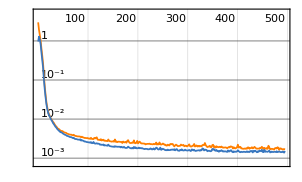
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:4950  rounds:495  time:28s  examples/s:182414
data | ,,  training examples:10000  validation examples:5000  processed examples:5068800  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:1.66×10^-3
validation | ,,  loss:1.52×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {2.08531,2.08531,2.08531,2.08531,2.08531,2.08531,2.08531,2.08531,2.08531,2.08531,2.80689,2.80689,2.80689,2.80689,2.80689,2.80689,2.80689,2.80689,2.80689,2.80689,2.58658,2.58658,2.58658,2.58658,2.58658,2.58658,2.58658,2.58658,2.58658,2.58658,2.83958,2.83958,2.83958,2.83958,2.83958,2.83958,2.83958,2.83958,2.83958,2.83958,2.03557,2.03557,2.03557,2.03557,2.03557,2.03557,2.03557,2.03557,2.03557,2.03557,2.6173,2.6173,2.6173,2.6173,2.6173,2.6173,2.6173,2.6173,2.6173,2.6173,2.53642,2.53642,2.53642,2.53642,2.53642,2.53642,2.53642,2.53642,2.53642,2.53642,2.68816,2.68816,2.68816,2.68816,2.68816,2.68816,2.68816,2.68816,2.68816,2.68816,2.01144,2.01144,2.01144,2.01144,2.01144,2.01144,2.01144,2.01144,2.01144,2.01144,2.02971,2.02971,2.02971,2.02971,2.02971,2.02971,2.02971,2.02971,2.02971,2.02971,2.71531,2.71531,2.71531,2.71531,2.71531,2.71531,2.71531,2.71531,2.71531,2.71531,2.69983,2.69983,2.69983,2.69983,2.69983,2.69983,2.69983,2.69983,2.69983,2.69983,2.23992,2.23992,2.23992,2.23992,2.23992,2.23992,2.23992,2.23992,2.23992,2.23992,2.82439,2.82439,2.82439,2.82439,2.82439,2.82439,2.82439,2.82439,2.82439,2.82439,2.3121,2.3121,2.3121,2.3121,2.3121,2.3121,2.3121,2.3121,2.3121,2.3121,2.64338,2.64338,2.64338,2.64338,2.64338,2.64338,2.64338,2.64338,2.64338,2.64338,2.02379,2.02379,2.02379,2.02379,2.02379,2.02379,2.02379,2.02379,2.02379,2.02379,2.71925,2.71925,2.71925,2.71925,2.71925,2.71925,2.71925,2.71925,2.71925,2.71925,2.68227,2.68227,2.68227,2.68227,2.68227,2.68227,2.68227,2.68227,2.68227,2.68227,2.56276,2.56276,2.56276,2.56276,2.56276,2.56276,2.56276,2.56276,2.56276,2.56276}

θ̂: {2.0504,2.14151,2.06211,2.1258,2.05955,2.12362,2.08436,2.08197,2.12703,2.10187,2.7693,2.76671,2.77567,2.81295,2.81658,2.86739,2.79718,2.81778,2.75808,2.83252,2.58651,2.54889,2.60726,2.59808,2.58207,2.59646,2.56045,2.59407,2.6227,2.60866,2.86219,2.88309,2.84169,2.81613,2.87425,2.84161,2.86555,2.86324,2.78838,2.84803,2.03507,2.02807,2.02796,2.03974,2.01388,2.03556,2.04823,2.09363,2.04332,2.04667,2.58583,2.62525,2.58444,2.55427,2.65477,2.65652,2.63125,2.64425,2.5744,2.5762,2.58902,2.50257,2.59119,2.56114,2.60247,2.541,2.49922,2.48994,2.56664,2.52624,2.74912,2.66447,2.74276,2.72685,2.68076,2.74017,2.71531,2.67279,2.7035,2.70869,2.03267,2.01339,2.02057,2.04344,2.06539,2.05708,2.05688,1.99599,2.0493,2.00909,2.02557,2.04903,2.02284,2.00347,2.03764,2.02718,2.00811,2.03157,2.0233,2.09326,2.7386,2.66785,2.70599,2.73186,2.7075,2.68935,2.7313,2.66675,2.68795,2.65875,2.63699,2.70666,2.6759,2.6741,2.73515,2.71642,2.68951,2.75284,2.67546,2.73265,2.15691,2.27142,2.25856,2.28408,2.29016,2.20556,2.25016,2.25654,2.21102,2.29028,2.759,2.80892,2.81959,2.84286,2.88556,2.83783,2.84095,2.81897,2.83177,2.8352,2.31091,2.33441,2.29409,2.37537,2.32656,2.2904,2.29754,2.33438,2.29439,2.35099,2.5999,2.7429,2.59687,2.64622,2.63655,2.69986,2.65769,2.60574,2.63768,2.68023,2.04897,2.05896,2.02302,2.02339,2.03163,2.02799,2.00773,2.03794,2.01001,2.03621,2.69799,2.65902,2.72612,2.73248,2.70697,2.70975,2.74735,2.75316,2.80779,2.71743,2.70863,2.68729,2.71122,2.71062,2.64585,2.72929,2.74037,2.7362,2.68783,2.66743,2.59883,2.54269,2.55262,2.56628,2.53345,2.60517,2.51307,2.61935,2.61382,2.53654}

abs(θ-θ̂): {0.0349119,0.0562029,0.0231979,0.0404842,0.0257621,0.0383134,0.000948433,0.00334549,0.0417161,0.0165606,0.0375905,0.0401783,0.0312114,0.00606229,0.00968959,0.0605066,0.00970171,0.0108953,0.0488097,0.0256355,0.0000730063,0.0376926,0.0206751,0.0114946,0.00451594,0.00988002,0.0261274,0.00749321,0.0361149,0.0220766,0.0226134,0.0435149,0.00211039,0.0234488,0.0346762,0.00203123,0.0259699,0.0236627,0.0511957,0.00845208,0.000500129,0.00749914,0.00761263,0.00417097,0.0216867,4.69508×10^-6,0.0126611,0.058061,0.00775464,0.0111044,0.0314766,0.00794737,0.0328673,0.0630382,0.0374664,0.0392148,0.0139476,0.026946,0.0429076,0.0411056,0.0525964,0.0338487,0.054767,0.0247227,0.066054,0.00458394,0.0371965,0.0464782,0.0302192,0.0101804,0.0609568,0.023687,0.0545965,0.0386899,0.00739636,0.0520133,0.0271467,0.0153662,0.0153409,0.0205332,0.0212292,0.00195234,0.00913685,0.0320026,0.0539579,0.0456416,0.0454459,0.0154436,0.0378629,0.00234825,0.00414346,0.0193138,0.00687549,0.0262463,0.00792839,0.00252888,0.021605,0.00185277,0.00641463,0.0635452,0.0232912,0.0474602,0.00931418,0.016554,0.00781238,0.0259596,0.0159882,0.0485591,0.0273617,0.0565609,0.0628437,0.00682891,0.0239338,0.0257381,0.0353152,0.0165907,0.0103265,0.0530092,0.0243744,0.0328115,0.0830167,0.0314941,0.0186352,0.0441553,0.0502407,0.0343636,0.010231,0.0166175,0.0289023,0.0503568,0.0653926,0.0154694,0.00480659,0.0184681,0.0611638,0.0134396,0.0165531,0.005426,0.00738232,0.0108108,0.00119426,0.0223033,0.0180116,0.0632686,0.0144577,0.021703,0.0145676,0.0222759,0.0177119,0.0388832,0.0434796,0.0995227,0.0465037,0.00284039,0.00682844,0.0564791,0.0143114,0.0376371,0.00569261,0.0368489,0.0251828,0.0351709,0.000771662,0.000401159,0.00783716,0.00420461,0.0160555,0.0141507,0.0137812,0.0124188,0.0212661,0.0602378,0.00686371,0.0132254,0.0122885,0.00950516,0.0280989,0.0339071,0.0885309,0.00182546,0.0263551,0.00501928,0.0289544,0.0283495,0.0364233,0.047022,0.0581034,0.0539306,0.00555501,0.01484,0.0360706,0.0200698,0.0101404,0.00351715,0.0293124,0.0424035,0.0496955,0.0565872,0.0510597,0.0262249}

RMSE:0.0330054

```mathematica
{Θ, e} = RunExperiment[PoissonDistribution, {2,3}];
```

### Geometric distribution

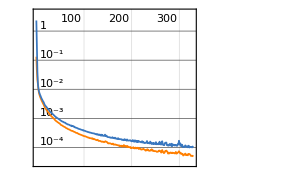
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3290  rounds:329  time:26s  examples/s:131467
data | ,,  training examples:10000  validation examples:5000  processed examples:3368960  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:5.4×10^-5
validation | ,,  loss:9.96×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {0.237757,0.237757,0.237757,0.237757,0.237757,0.237757,0.237757,0.237757,0.237757,0.237757,0.259274,0.259274,0.259274,0.259274,0.259274,0.259274,0.259274,0.259274,0.259274,0.259274,0.209887,0.209887,0.209887,0.209887,0.209887,0.209887,0.209887,0.209887,0.209887,0.209887,0.213921,0.213921,0.213921,0.213921,0.213921,0.213921,0.213921,0.213921,0.213921,0.213921,0.270373,0.270373,0.270373,0.270373,0.270373,0.270373,0.270373,0.270373,0.270373,0.270373,0.289269,0.289269,0.289269,0.289269,0.289269,0.289269,0.289269,0.289269,0.289269,0.289269,0.234873,0.234873,0.234873,0.234873,0.234873,0.234873,0.234873,0.234873,0.234873,0.234873,0.250011,0.250011,0.250011,0.250011,0.250011,0.250011,0.250011,0.250011,0.250011,0.250011,0.252443,0.252443,0.252443,0.252443,0.252443,0.252443,0.252443,0.252443,0.252443,0.252443,0.229539,0.229539,0.229539,0.229539,0.229539,0.229539,0.229539,0.229539,0.229539,0.229539,0.252998,0.252998,0.252998,0.252998,0.252998,0.252998,0.252998,0.252998,0.252998,0.252998,0.284606,0.284606,0.284606,0.284606,0.284606,0.284606,0.284606,0.284606,0.284606,0.284606,0.2518,0.2518,0.2518,0.2518,0.2518,0.2518,0.2518,0.2518,0.2518,0.2518,0.28917,0.28917,0.28917,0.28917,0.28917,0.28917,0.28917,0.28917,0.28917,0.28917,0.247848,0.247848,0.247848,0.247848,0.247848,0.247848,0.247848,0.247848,0.247848,0.247848,0.235497,0.235497,0.235497,0.235497,0.235497,0.235497,0.235497,0.235497,0.235497,0.235497,0.253076,0.253076,0.253076,0.253076,0.253076,0.253076,0.253076,0.253076,0.253076,0.253076,0.208009,0.208009,0.208009,0.208009,0.208009,0.208009,0.208009,0.208009,0.208009,0.208009,0.249476,0.249476,0.249476,0.249476,0.249476,0.249476,0.249476,0.249476,0.249476,0.249476,0.204821,0.204821,0.204821,0.204821,0.204821,0.204821,0.204821,0.204821,0.204821,0.204821}

θ̂: {0.248429,0.242221,0.22458,0.240755,0.246843,0.254467,0.234816,0.212922,0.249844,0.228185,0.26043,0.252475,0.266111,0.257853,0.252925,0.260061,0.253876,0.233609,0.265922,0.264979,0.207864,0.209081,0.212414,0.210668,0.214403,0.216066,0.210705,0.212275,0.207191,0.201837,0.205069,0.211209,0.215,0.218661,0.214093,0.218175,0.217646,0.222467,0.214367,0.209891,0.258969,0.269177,0.272349,0.289116,0.266533,0.268151,0.271552,0.274457,0.267395,0.275234,0.296318,0.287661,0.287366,0.287925,0.290367,0.283908,0.293641,0.281074,0.293847,0.289133,0.232927,0.232572,0.230164,0.252142,0.227111,0.234126,0.213348,0.217098,0.233062,0.247297,0.24089,0.238337,0.219988,0.245971,0.282185,0.241054,0.253259,0.238696,0.252244,0.244687,0.238139,0.268226,0.234528,0.256395,0.250944,0.236521,0.253431,0.260048,0.249767,0.261182,0.231105,0.229222,0.228393,0.224683,0.237518,0.233757,0.2304,0.244865,0.2239,0.230247,0.2523,0.258052,0.263531,0.257899,0.259356,0.255437,0.240134,0.25709,0.243416,0.275821,0.285761,0.288968,0.280815,0.283074,0.29504,0.290825,0.289328,0.276257,0.286854,0.276675,0.249599,0.25602,0.28871,0.236494,0.255098,0.247621,0.281957,0.243121,0.253489,0.237883,0.288768,0.317332,0.293667,0.288107,0.286238,0.276694,0.288103,0.288467,0.276149,0.283213,0.243945,0.223666,0.262893,0.258918,0.237106,0.248734,0.254665,0.209429,0.268304,0.278581,0.232295,0.241359,0.244523,0.245961,0.250205,0.266431,0.221473,0.235136,0.246037,0.219518,0.252688,0.251168,0.264908,0.244406,0.253271,0.262961,0.254372,0.268304,0.257717,0.26936,0.209268,0.205562,0.202006,0.209846,0.21725,0.210089,0.217661,0.215181,0.206637,0.207893,0.260962,0.245659,0.248058,0.235868,0.255627,0.225036,0.248121,0.258556,0.256813,0.261483,0.20823,0.211753,0.208147,0.213187,0.211375,0.209891,0.209005,0.209237,0.215317,0.211692}

abs(θ-θ̂): {0.0106713,0.00446359,0.0131771,0.0029981,0.00908606,0.0167092,0.00294117,0.0248356,0.0120865,0.0095721,0.00115622,0.00679886,0.00683797,0.00142037,0.00634842,0.000787891,0.00539722,0.0256646,0.00664882,0.00570581,0.00202294,0.000806295,0.00252718,0.000781245,0.0045161,0.00617861,0.000817738,0.00238787,0.00269646,0.00805061,0.00885186,0.00271209,0.00107906,0.00474004,0.0001717,0.00425375,0.00372499,0.00854593,0.000445583,0.00403062,0.0114041,0.00119678,0.00197583,0.0187423,0.00384021,0.00222293,0.00117811,0.00408381,0.00297878,0.00486054,0.00704911,0.00160709,0.00190297,0.00134325,0.0010983,0.00536028,0.0043723,0.00819418,0.00457823,0.000135931,0.00194589,0.00230106,0.00470873,0.0172694,0.00776225,0.000746646,0.0215251,0.0177748,0.00181053,0.0124247,0.00912074,0.0116742,0.0300234,0.00404007,0.0321739,0.0089575,0.00324771,0.011315,0.00223261,0.00532378,0.0143041,0.0157834,0.0179152,0.00395196,0.00149918,0.0159215,0.000988716,0.00760573,0.00267606,0.00873917,0.00156546,0.000317694,0.00114629,0.00485632,0.0079782,0.00421737,0.000860258,0.0153252,0.00563958,0.000707193,0.000698296,0.00505334,0.0105327,0.00490037,0.00635758,0.00243807,0.012864,0.00409162,0.00958271,0.0228223,0.00115491,0.0043623,0.00379099,0.00153126,0.0104345,0.00621976,0.00472234,0.00834902,0.00224809,0.00793063,0.00220098,0.0042205,0.0369106,0.0153055,0.00329865,0.004179,0.030157,0.00867862,0.00168936,0.0139172,0.000402191,0.0281622,0.00449683,0.00106267,0.00293259,0.012476,0.00106765,0.000703612,0.0130216,0.00595743,0.00390349,0.0241824,0.0150448,0.0110694,0.0107421,0.000885967,0.00681685,0.0384195,0.0204562,0.0307331,0.00320197,0.00586218,0.00902605,0.0104632,0.014708,0.0309337,0.014024,0.000360933,0.0105398,0.0159796,0.000388261,0.00190752,0.0118325,0.00867025,0.000195,0.00988514,0.00129632,0.0152284,0.00464133,0.0162842,0.00125839,0.00244726,0.00600372,0.00183641,0.00924081,0.0020796,0.00965199,0.00717129,0.0013723,0.00011627,0.0114852,0.0038178,0.00141829,0.0136086,0.00615081,0.0244406,0.00135565,0.00907931,0.00733691,0.0120063,0.00340892,0.00693238,0.0033264,0.00836578,0.00655429,0.00507043,0.00418419,0.00441577,0.0104964,0.0068711}

RMSE:0.0107123

```mathematica
{Θ, e} = RunExperiment[GeometricDistribution, {0.2,0.3}];
```

### Normal distribution

```mathematica
NormalDistribution1D[σ_]:=NormalDistribution[0,σ];
```

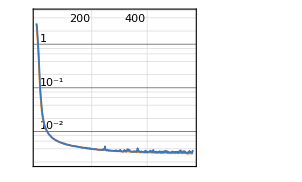
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5660  rounds:566  time:37s  examples/s:159843
data | ,,  training examples:10000  validation examples:5000  processed examples:5795840  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:3.29×10^-3
validation | ,,  loss:3.47×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {2.20364,2.20364,2.20364,2.20364,2.20364,2.20364,2.20364,2.20364,2.20364,2.20364,2.00496,2.00496,2.00496,2.00496,2.00496,2.00496,2.00496,2.00496,2.00496,2.00496,2.23711,2.23711,2.23711,2.23711,2.23711,2.23711,2.23711,2.23711,2.23711,2.23711,2.54076,2.54076,2.54076,2.54076,2.54076,2.54076,2.54076,2.54076,2.54076,2.54076,2.66701,2.66701,2.66701,2.66701,2.66701,2.66701,2.66701,2.66701,2.66701,2.66701,2.39293,2.39293,2.39293,2.39293,2.39293,2.39293,2.39293,2.39293,2.39293,2.39293,2.46611,2.46611,2.46611,2.46611,2.46611,2.46611,2.46611,2.46611,2.46611,2.46611,2.37604,2.37604,2.37604,2.37604,2.37604,2.37604,2.37604,2.37604,2.37604,2.37604,2.07799,2.07799,2.07799,2.07799,2.07799,2.07799,2.07799,2.07799,2.07799,2.07799,2.83018,2.83018,2.83018,2.83018,2.83018,2.83018,2.83018,2.83018,2.83018,2.83018,2.34531,2.34531,2.34531,2.34531,2.34531,2.34531,2.34531,2.34531,2.34531,2.34531,2.57594,2.57594,2.57594,2.57594,2.57594,2.57594,2.57594,2.57594,2.57594,2.57594,2.59404,2.59404,2.59404,2.59404,2.59404,2.59404,2.59404,2.59404,2.59404,2.59404,2.86914,2.86914,2.86914,2.86914,2.86914,2.86914,2.86914,2.86914,2.86914,2.86914,2.92766,2.92766,2.92766,2.92766,2.92766,2.92766,2.92766,2.92766,2.92766,2.92766,2.88877,2.88877,2.88877,2.88877,2.88877,2.88877,2.88877,2.88877,2.88877,2.88877,2.24746,2.24746,2.24746,2.24746,2.24746,2.24746,2.24746,2.24746,2.24746,2.24746,2.17566,2.17566,2.17566,2.17566,2.17566,2.17566,2.17566,2.17566,2.17566,2.17566,2.36813,2.36813,2.36813,2.36813,2.36813,2.36813,2.36813,2.36813,2.36813,2.36813,2.79761,2.79761,2.79761,2.79761,2.79761,2.79761,2.79761,2.79761,2.79761,2.79761}

θ̂: {2.1949,2.24999,2.21478,2.30061,2.17707,2.17659,2.27725,2.15372,2.2519,2.22145,2.02879,2.03392,2.0524,2.05253,2.01149,2.03153,2.02084,2.00509,2.00879,2.01814,2.12199,2.21003,2.27804,2.26498,2.25256,2.23765,2.14805,2.19225,2.20667,2.26526,2.53081,2.57904,2.57142,2.56297,2.5344,2.50556,2.50722,2.50705,2.64801,2.39056,2.65402,2.64428,2.63,2.67947,2.64784,2.61276,2.62981,2.67398,2.64068,2.70365,2.45832,2.36781,2.38153,2.38039,2.42733,2.47581,2.39831,2.38196,2.41619,2.37023,2.53077,2.4546,2.53337,2.66266,2.48559,2.41232,2.33844,2.49874,2.52205,2.53018,2.32631,2.44454,2.29993,2.44182,2.43449,2.28917,2.30928,2.41621,2.44948,2.25738,2.04474,2.17079,2.12345,2.08568,2.03757,2.03708,2.06883,1.99917,2.053,2.08907,2.81986,2.76693,2.75693,2.82795,2.82716,2.81337,2.73455,2.91197,2.83662,2.92679,2.312,2.25955,2.27463,2.31755,2.32872,2.35982,2.30144,2.27492,2.40113,2.36593,2.75552,2.67625,2.56613,2.59815,2.51072,2.61052,2.62542,2.57215,2.68192,2.54672,2.55768,2.53974,2.58849,2.55574,2.63912,2.58379,2.70677,2.66361,2.55395,2.51425,2.81398,2.87046,2.89704,2.84954,2.87343,2.81469,2.83824,2.86984,2.81364,2.92465,2.85232,2.94372,2.85115,2.86374,2.8892,2.83084,2.90702,2.89508,3.03374,2.90304,2.87981,2.95813,2.8282,2.90285,2.89753,2.86047,2.89924,2.90574,2.8919,2.88917,2.2544,2.27028,2.19527,2.25461,2.22807,2.18227,2.20522,2.17181,2.24646,2.35334,2.22876,2.15845,2.15579,2.20462,2.1718,2.25053,2.05808,2.22724,2.13353,2.19625,2.3245,2.4421,2.5592,2.45143,2.39241,2.40214,2.4333,2.50462,2.37338,2.3739,2.73055,2.87794,2.75004,2.81646,2.80747,2.82974,2.87967,2.80121,2.78651,2.72248}

abs(θ-θ̂): {0.0087449,0.0463536,0.0111359,0.0969651,0.0265688,0.0270519,0.0736085,0.0499257,0.0482593,0.0178133,0.0238319,0.0289691,0.0474398,0.0475698,0.00653723,0.0265744,0.0158892,0.000138309,0.00383404,0.0131848,0.115122,0.0270876,0.0409318,0.0278655,0.0154427,0.00053677,0.0890621,0.0448653,0.0304448,0.0281497,0.00995381,0.0382723,0.0306598,0.0222027,0.00636799,0.0352076,0.0335484,0.0337103,0.10725,0.150202,0.0129834,0.0227237,0.0370057,0.012464,0.0191629,0.0542477,0.0371945,0.00697823,0.0263253,0.0366449,0.0653839,0.0251203,0.0114005,0.0125401,0.0343942,0.0828769,0.00538131,0.0109742,0.023261,0.022697,0.0646693,0.0115085,0.0672666,0.19655,0.0194837,0.0537859,0.127667,0.0326387,0.0559427,0.0640797,0.0497282,0.0685091,0.0761097,0.0657818,0.0584597,0.0868655,0.0667503,0.040173,0.07344,0.118659,0.033244,0.0928008,0.0454594,0.0076956,0.0404137,0.0409113,0.00916155,0.0788189,0.0249887,0.0110835,0.0103197,0.0632506,0.0732546,0.00222949,0.0030177,0.0168081,0.0956283,0.0817918,0.00644323,0.0966093,0.0333085,0.0857601,0.0706749,0.0277577,0.0165837,0.0145147,0.0438667,0.0703881,0.0558266,0.020628,0.179582,0.10031,0.0098094,0.0222114,0.0652119,0.0345853,0.0494874,0.00378171,0.105986,0.0292203,0.0363604,0.054295,0.00555148,0.0383021,0.0450815,0.0102507,0.112729,0.0695697,0.0400874,0.0797845,0.0551547,0.00132524,0.0278982,0.0195967,0.00429474,0.054454,0.0308987,0.000696767,0.0555016,0.0555144,0.0753401,0.0160603,0.0765029,0.0639139,0.038453,0.0968178,0.0206362,0.032579,0.106084,0.0246118,0.00895721,0.0693573,0.0605667,0.0140812,0.00875896,0.0283034,0.010471,0.016972,0.00313299,0.000402147,0.00693892,0.0228224,0.0521834,0.00714873,0.0193827,0.0651915,0.0422411,0.0756433,0.000996842,0.105881,0.0530988,0.0172106,0.0198735,0.0289527,0.00386536,0.0748671,0.117589,0.0515763,0.0421323,0.0205845,0.0436264,0.073969,0.191068,0.0832993,0.0242781,0.034011,0.065173,0.136486,0.00524939,0.00576509,0.06706,0.0803268,0.0475752,0.0188513,0.00985717,0.0321231,0.0820563,0.00360011,0.0111022,0.0751367}

RMSE:0.0571615

```mathematica
{Θ, e} = RunExperiment[NormalDistribution1D, {2,3}];
```